```mathematica
Subsets[Range[6],{5}]
```

{{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6}}

```mathematica
EdgeCountSubGraph[g_]:=Block[{fives=Subsets[VertexList[g],{5}],all=VertexList[g],toRemove,h},
Table[
toRemove=Select[all,!MemberQ[five,#]&];
h=VertexDelete[g,toRemove];
five-> EdgeCount[h]
,
{five,fives}
]
]
```

```mathematica
Monitor[
Multicolumn[
Table[
With[{g=Graph[plantri[[k]]]},{VertexCount[g],EdgeCount[g]}
],
{k,4,100}
]
],
k
]
```

{16,42} | {18,48} | {19,51} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{16,42} | {18,48} | {19,51} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{16,42} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{17,45} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{17,45} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{17,45} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{17,45} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54}
{18,48} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | 
{18,48} | {18,48} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} | 
{18,48} | {19,51} | {19,51} | {19,51} | {20,54} | {20,54} | {20,54} | {20,54} | {20,54} |

```mathematica
Monitor[
TableForm[
Table[
PadLeft[Sort[Tally[Map[#[[2]]&,EdgeCountSubGraph[Graph[plantri[[k]]]]]]],10],
{k,1,100}
],
TableDepth->2
],
k
]
```

0 | 0 | 0 | 0 | 0 | {3,120} | {4,300} | {5,252} | {6,60} | {7,60}
0 | 0 | 0 | 0 | {2,156} | {3,604} | {4,660} | {5,408} | {6,102} | {7,72}
0 | 0 | 0 | {1,24} | {2,378} | {3,1005} | {4,900} | {5,495} | {6,123} | {7,78}
0 | 0 | 0 | {1,96} | {2,744} | {3,1536} | {4,1176} | {5,588} | {6,144} | {7,84}
0 | 0 | 0 | {1,84} | {2,772} | {3,1524} | {4,1164} | {5,596} | {6,144} | {7,84}
0 | 0 | 0 | {1,98} | {2,812} | {3,1442} | {4,1162} | {5,616} | {6,154} | {7,84}
0 | 0 | {0,4} | {1,229} | {2,1342} | {3,2185} | {4,1478} | {5,695} | {6,165} | {7,90}
0 | 0 | {0,4} | {1,222} | {2,1359} | {3,2176} | {4,1473} | {5,699} | {6,165} | {7,90}
0 | 0 | {0,6} | {1,230} | {2,1376} | {3,2130} | {4,1477} | {5,709} | {6,170} | {7,90}
0 | 0 | {0,5} | {1,205} | {2,1395} | {3,2160} | {4,1460} | {5,708} | {6,165} | {7,90}
0 | 0 | {0,12} | {1,480} | {2,2208} | {3,2964} | {4,1806} | {5,816} | {6,186} | {7,96}
0 | 0 | {0,18} | {1,480} | {2,2184} | {3,2976} | {4,1824} | {5,804} | {6,186} | {7,96}
0 | 0 | {0,16} | {1,491} | {2,2217} | {3,2917} | {4,1814} | {5,826} | {6,191} | {7,96}
0 | 0 | {0,20} | {1,499} | {2,2181} | {3,2937} | {4,1830} | {5,814} | {6,191} | {7,96}
0 | 0 | {0,26} | {1,502} | {2,2202} | {3,2882} | {4,1840} | {5,824} | {6,196} | {7,96}
0 | 0 | {0,18} | {1,510} | {2,2214} | {3,2878} | {4,1820} | {5,836} | {6,196} | {7,96}
0 | 0 | {0,16} | {1,480} | {2,2192} | {3,2972} | {4,1818} | {5,808} | {6,186} | {7,96}
0 | 0 | {0,18} | {1,456} | {2,2244} | {3,2940} | {4,1812} | {5,816} | {6,186} | {7,96}
0 | 0 | {0,16} | {1,464} | {2,2232} | {3,2948} | {4,1810} | {5,816} | {6,186} | {7,96}
0 | 0 | {0,16} | {1,472} | {2,2212} | {3,2960} | {4,1814} | {5,812} | {6,186} | {7,96}
0 | 0 | {0,20} | {1,592} | {2,2216} | {3,2704} | {4,1844} | {5,880} | {6,216} | {7,96}
0 | 0 | {0,22} | {1,488} | {2,2250} | {3,2862} | {4,1812} | {5,842} | {6,196} | {7,96}
0 | 0 | {0,49} | {1,946} | {2,3338} | {3,3817} | {4,2204} | {5,955} | {6,217} | {7,102}
0 | 0 | {0,42} | {1,894} | {2,3376} | {3,3885} | {4,2187} | {5,935} | {6,207} | {7,102}
0 | 0 | {0,45} | {1,900} | {2,3348} | {3,3903} | {4,2196} | {5,927} | {6,207} | {7,102}
0 | 0 | {0,45} | {1,900} | {2,3348} | {3,3903} | {4,2196} | {5,927} | {6,207} | {7,102}
0 | 0 | {0,49} | {1,906} | {2,3378} | {3,3837} | {4,2199} | {5,945} | {6,212} | {7,102}
0 | 0 | {0,53} | {1,948} | {2,3316} | {3,3831} | {4,2214} | {5,947} | {6,217} | {7,102}
0 | 0 | {0,44} | {1,904} | {2,3342} | {3,3907} | {4,2195} | {5,927} | {6,207} | {7,102}
0 | 0 | {0,47} | {1,901} | {2,3337} | {3,3910} | {4,2201} | {5,923} | {6,207} | {7,102}
0 | 0 | {0,46} | {1,896} | {2,3354} | {3,3899} | {4,2197} | {5,927} | {6,207} | {7,102}
0 | 0 | {0,66} | {1,963} | {2,3285} | {3,3804} | {4,2241} | {5,945} | {6,222} | {7,102}
0 | 0 | {0,53} | {1,926} | {2,3310} | {3,3881} | {4,2215} | {5,929} | {6,212} | {7,102}
0 | 0 | {0,51} | {1,925} | {2,3321} | {3,3874} | {4,2210} | {5,933} | {6,212} | {7,102}
0 | 0 | {0,49} | {1,915} | {2,3355} | {3,3852} | {4,2202} | {5,941} | {6,212} | {7,102}
0 | 0 | {0,52} | {1,934} | {2,3356} | {3,3805} | {4,2207} | {5,955} | {6,217} | {7,102}
0 | 0 | {0,54} | {1,935} | {2,3345} | {3,3812} | {4,2212} | {5,951} | {6,217} | {7,102}
0 | 0 | {0,46} | {1,927} | {2,3337} | {3,3864} | {4,2199} | {5,941} | {6,212} | {7,102}
0 | 0 | {0,48} | {1,928} | {2,3326} | {3,3871} | {4,2204} | {5,937} | {6,212} | {7,102}
0 | 0 | {0,48} | {1,919} | {2,3349} | {3,3856} | {4,2201} | {5,941} | {6,212} | {7,102}
0 | 0 | {0,52} | {1,964} | {2,3344} | {3,3761} | {4,2216} | {5,967} | {6,222} | {7,102}
0 | 0 | {0,56} | {1,988} | {2,3328} | {3,3725} | {4,2225} | {5,977} | {6,227} | {7,102}
0 | 0 | {0,45} | {1,905} | {2,3396} | {3,3829} | {4,2185} | {5,954} | {6,212} | {7,102}
0 | 0 | {0,51} | {1,914} | {2,3407} | {3,3782} | {4,2185} | {5,970} | {6,217} | {7,102}
0 | 0 | {0,67} | {1,979} | {2,3361} | {3,3670} | {4,2222} | {5,995} | {6,232} | {7,102}
0 | 0 | {0,112} | {1,1620} | {2,4798} | {3,4924} | {4,2628} | {5,1076} | {6,238} | {7,108}
0 | 0 | {0,127} | {1,1669} | {2,4753} | {3,4845} | {4,2660} | {5,1094} | {6,248} | {7,108}
0 | 0 | {0,118} | {1,1596} | {2,4834} | {3,4900} | {4,2634} | {5,1076} | {6,238} | {7,108}
0 | 0 | {0,127} | {1,1615} | {2,4818} | {3,4859} | {4,2648} | {5,1086} | {6,243} | {7,108}
0 | 0 | {0,115} | {1,1677} | {2,4785} | {3,4821} | {4,2640} | {5,1110} | {6,248} | {7,108}
0 | 0 | {0,106} | {1,1614} | {2,4840} | {3,4894} | {4,2616} | {5,1088} | {6,238} | {7,108}
0 | 0 | {0,115} | {1,1583} | {2,4808} | {3,4971} | {4,2632} | {5,1054} | {6,233} | {7,108}
0 | 0 | {0,108} | {1,1606} | {2,4852} | {3,4886} | {4,2618} | {5,1088} | {6,238} | {7,108}
0 | 0 | {0,97} | {1,1560} | {2,4874} | {3,4976} | {4,2601} | {5,1060} | {6,228} | {7,108}
0 | 0 | {0,105} | {1,1573} | {2,4878} | {3,4921} | {4,2612} | {5,1074} | {6,233} | {7,108}
0 | 0 | {0,100} | {1,1548} | {2,4892} | {3,4964} | {4,2604} | {5,1060} | {6,228} | {7,108}
0 | 0 | {0,118} | {1,1606} | {2,4808} | {3,4918} | {4,2636} | {5,1072} | {6,238} | {7,108}
0 | 0 | {0,120} | {1,1598} | {2,4820} | {3,4910} | {4,2638} | {5,1072} | {6,238} | {7,108}
0 | 0 | {0,111} | {1,1579} | {2,4836} | {3,4951} | {4,2624} | {5,1062} | {6,233} | {7,108}
0 | 0 | {0,112} | {1,1585} | {2,4816} | {3,4965} | {4,2627} | {5,1058} | {6,233} | {7,108}
0 | 0 | {0,113} | {1,1581} | {2,4822} | {3,4961} | {4,2628} | {5,1058} | {6,233} | {7,108}
0 | 0 | {0,110} | {1,1548} | {2,4848} | {3,4996} | {4,2622} | {5,1044} | {6,228} | {7,108}
0 | 0 | {0,116} | {1,1614} | {2,4796} | {3,4926} | {4,2634} | {5,1072} | {6,238} | {7,108}
0 | 0 | {0,108} | {1,1556} | {2,4836} | {3,5004} | {4,2620} | {5,1044} | {6,228} | {7,108}
0 | 0 | {0,118} | {1,1616} | {2,4782} | {3,4936} | {4,2638} | {5,1068} | {6,238} | {7,108}
0 | 0 | {0,124} | {1,1612} | {2,4766} | {3,4948} | {4,2648} | {5,1060} | {6,238} | {7,108}
0 | 0 | {0,104} | {1,1562} | {2,4838} | {3,5002} | {4,2614} | {5,1048} | {6,228} | {7,108}
0 | 0 | {0,104} | {1,1562} | {2,4838} | {3,5002} | {4,2614} | {5,1048} | {6,228} | {7,108}
0 | 0 | {0,104} | {1,1552} | {2,4864} | {3,4984} | {4,2612} | {5,1052} | {6,228} | {7,108}
0 | 0 | {0,109} | {1,1567} | {2,4876} | {3,4923} | {4,2618} | {5,1070} | {6,233} | {7,108}
0 | 0 | {0,112} | {1,1610} | {2,4824} | {3,4906} | {4,2626} | {5,1080} | {6,238} | {7,108}
0 | 0 | {0,120} | {1,1668} | {2,4784} | {3,4828} | {4,2640} | {5,1108} | {6,248} | {7,108}
0 | 0 | {0,105} | {1,1583} | {2,4852} | {3,4939} | {4,2614} | {5,1070} | {6,233} | {7,108}
0 | 0 | {0,112} | {1,1600} | {2,4850} | {3,4888} | {4,2624} | {5,1084} | {6,238} | {7,108}
0 | 0 | {0,110} | {1,1583} | {2,4830} | {3,4955} | {4,2623} | {5,1062} | {6,233} | {7,108}
0 | 0 | {0,116} | {1,1614} | {2,4796} | {3,4926} | {4,2634} | {5,1072} | {6,238} | {7,108}
0 | 0 | {0,102} | {1,1630} | {2,4816} | {3,4910} | {4,2612} | {5,1088} | {6,238} | {7,108}
0 | 0 | {0,101} | {1,1554} | {2,4872} | {3,4978} | {4,2607} | {5,1056} | {6,228} | {7,108}
0 | 0 | {0,106} | {1,1589} | {2,4832} | {3,4953} | {4,2617} | {5,1066} | {6,233} | {7,108}
0 | 0 | {0,108} | {1,1591} | {2,4818} | {3,4963} | {4,2621} | {5,1062} | {6,233} | {7,108}
0 | 0 | {0,102} | {1,1560} | {2,4852} | {3,4992} | {4,2610} | {5,1052} | {6,228} | {7,108}
0 | 0 | {0,102} | {1,1560} | {2,4852} | {3,4992} | {4,2610} | {5,1052} | {6,228} | {7,108}
0 | 0 | {0,128} | {1,1631} | {2,4772} | {3,4891} | {4,2653} | {5,1078} | {6,243} | {7,108}
0 | 0 | {0,109} | {1,1587} | {2,4824} | {3,4959} | {4,2622} | {5,1062} | {6,233} | {7,108}
0 | 0 | {0,106} | {1,1554} | {2,4850} | {3,4994} | {4,2616} | {5,1048} | {6,228} | {7,108}
0 | 0 | {0,118} | {1,1616} | {2,4782} | {3,4936} | {4,2638} | {5,1068} | {6,238} | {7,108}
0 | 0 | {0,102} | {1,1560} | {2,4852} | {3,4992} | {4,2610} | {5,1052} | {6,228} | {7,108}
0 | 0 | {0,98} | {1,1566} | {2,4854} | {3,4990} | {4,2604} | {5,1056} | {6,228} | {7,108}
0 | 0 | {0,106} | {1,1579} | {2,4858} | {3,4935} | {4,2615} | {5,1070} | {6,233} | {7,108}
0 | 0 | {0,119} | {1,1602} | {2,4814} | {3,4914} | {4,2637} | {5,1072} | {6,238} | {7,108}
0 | 0 | {0,96} | {1,1564} | {2,4868} | {3,4980} | {4,2600} | {5,1060} | {6,228} | {7,108}
0 | 0 | {0,96} | {1,1544} | {2,4920} | {3,4944} | {4,2596} | {5,1068} | {6,228} | {7,108}
0 | 0 | {0,104} | {1,1567} | {2,4898} | {3,4907} | {4,2609} | {5,1078} | {6,233} | {7,108}
0 | 0 | {0,102} | {1,1595} | {2,4834} | {3,4951} | {4,2611} | {5,1070} | {6,233} | {7,108}
0 | 0 | {0,110} | {1,1618} | {2,4812} | {3,4914} | {4,2624} | {5,1080} | {6,238} | {7,108}
0 | 0 | {0,108} | {1,1616} | {2,4826} | {3,4904} | {4,2620} | {5,1084} | {6,238} | {7,108}
0 | 0 | {0,103} | {1,1581} | {2,4866} | {3,4929} | {4,2610} | {5,1074} | {6,233} | {7,108}
0 | 0 | {0,108} | {1,1606} | {2,4852} | {3,4886} | {4,2618} | {5,1088} | {6,238} | {7,108}
0 | 0 | {0,114} | {1,1592} | {2,4862} | {3,4880} | {4,2626} | {5,1084} | {6,238} | {7,108}
0 | 0 | {0,126} | {1,1732} | {2,4742} | {3,4740} | {4,2666} | {5,1132} | {6,258} | {7,108}

```mathematica
Monitor[
TableForm[
Table[
PadLeft[Sort[Tally[Map[#[[2]]&,EdgeCountSubGraph[GraphComplement[MinimalGraph[k]]]]]],10],
{k,1,20}
],
TableDepth->2
],
k
]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {1,1}
0 | 0 | 0 | 0 | 0 | 0 | 0 | {1,2} | {2,2} | {3,2}
0 | 0 | 0 | 0 | 0 | {1,3} | {2,6} | {3,5} | {4,6} | {6,1}
0 | 0 | 0 | {1,4} | {2,12} | {3,10} | {4,18} | {5,6} | {6,2} | {7,4}
0 | 0 | {1,5} | {2,20} | {3,18} | {4,36} | {5,24} | {6,5} | {7,12} | {8,6}
0 | {1,6} | {2,30} | {3,30} | {4,60} | {5,60} | {6,14} | {7,24} | {8,24} | {9,4}
{1,7} | {2,42} | {3,47} | {4,90} | {5,120} | {6,35} | {7,40} | {8,60} | {9,20} | {10,1}
{1,8} | {2,56} | {3,70} | {4,126} | {5,210} | {6,76} | {7,60} | {8,120} | {9,60} | {10,6}
{1,9} | {2,72} | {3,100} | {4,168} | {5,336} | {6,147} | {7,84} | {8,210} | {9,140} | {10,21}
{1,10} | {2,90} | {3,138} | {4,216} | {5,504} | {6,260} | {7,112} | {8,336} | {9,280} | {10,56}
{1,11} | {2,110} | {3,185} | {4,270} | {5,720} | {6,429} | {7,144} | {8,504} | {9,504} | {10,126}
{1,12} | {2,132} | {3,242} | {4,330} | {5,990} | {6,670} | {7,180} | {8,720} | {9,840} | {10,252}
{1,13} | {2,156} | {3,310} | {4,396} | {5,1320} | {6,1001} | {7,220} | {8,990} | {9,1320} | {10,462}
{1,14} | {2,182} | {3,390} | {4,468} | {5,1716} | {6,1442} | {7,264} | {8,1320} | {9,1980} | {10,792}
{1,15} | {2,210} | {3,483} | {4,546} | {5,2184} | {6,2015} | {7,312} | {8,1716} | {9,2860} | {10,1287}
{1,16} | {2,240} | {3,590} | {4,630} | {5,2730} | {6,2744} | {7,364} | {8,2184} | {9,4004} | {10,2002}
{1,17} | {2,272} | {3,712} | {4,720} | {5,3360} | {6,3655} | {7,420} | {8,2730} | {9,5460} | {10,3003}

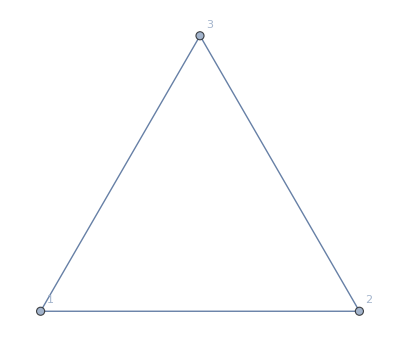
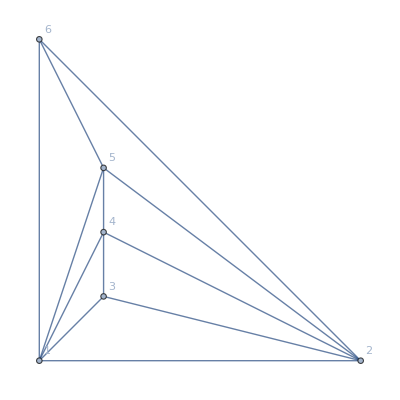
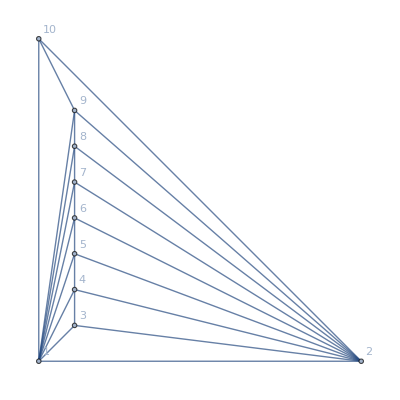
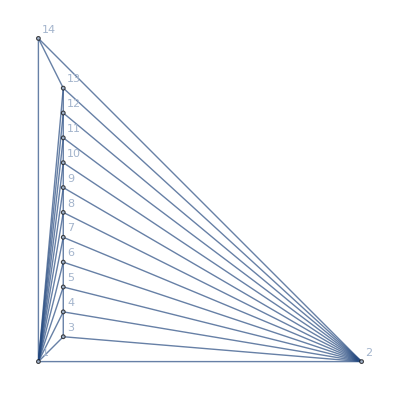
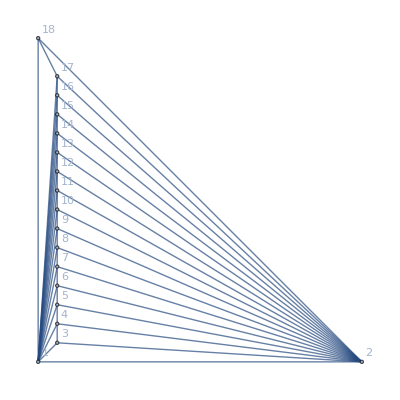
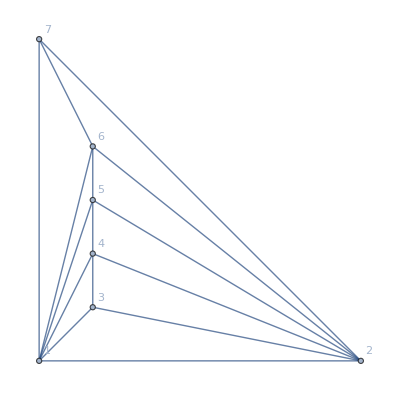
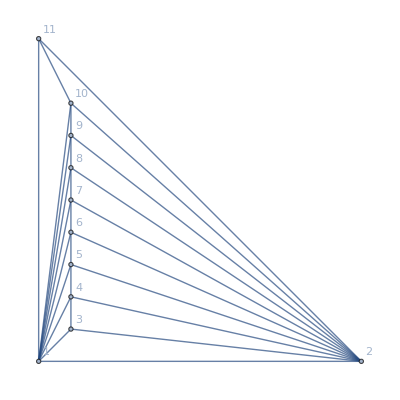
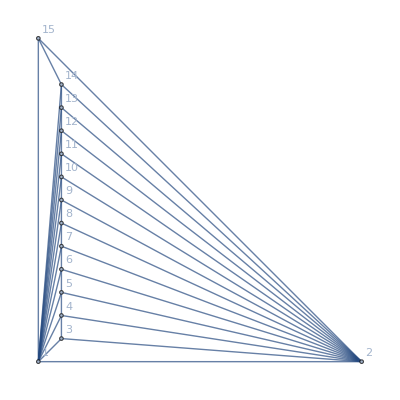
-Graphics-1 | -Graphics-5 | -Graphics-9 | -Graphics-13 | -Graphics-17
-Graphics-2 | -Graphics-6 | -Graphics-10 | -Graphics-14 | -Graphics-18
-Graphics-3 | -Graphics-7 | -Graphics-11 | -Graphics-15 | -Graphics-19
-Graphics-4 | -Graphics-8 | -Graphics-12 | -Graphics-16 | -Graphics-20

```mathematica
Multicolumn[
Table[
Labeled[MinimalGraph[k],k],
{k,1,20}
]
]
```

```mathematica
Monitor[
TableForm[
Table[
PadLeft[Sort[Tally[Map[#[[2]]&,EdgeCountSubGraph[MinimalGraph[k]]]]],10],
{k,1,20}
],
TableDepth->2
],
k
]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {9,1}
0 | 0 | 0 | 0 | 0 | 0 | 0 | {7,2} | {8,2} | {9,2}
0 | 0 | 0 | 0 | 0 | {4,1} | {6,6} | {7,5} | {8,6} | {9,3}
0 | 0 | 0 | {3,4} | {4,2} | {5,6} | {6,18} | {7,10} | {8,12} | {9,4}
0 | 0 | {2,6} | {3,12} | {4,5} | {5,24} | {6,36} | {7,18} | {8,20} | {9,5}
0 | {1,4} | {2,24} | {3,24} | {4,14} | {5,60} | {6,60} | {7,30} | {8,30} | {9,6}
{0,1} | {1,20} | {2,60} | {3,40} | {4,35} | {5,120} | {6,90} | {7,47} | {8,42} | {9,7}
{0,6} | {1,60} | {2,120} | {3,60} | {4,76} | {5,210} | {6,126} | {7,70} | {8,56} | {9,8}
{0,21} | {1,140} | {2,210} | {3,84} | {4,147} | {5,336} | {6,168} | {7,100} | {8,72} | {9,9}
{0,56} | {1,280} | {2,336} | {3,112} | {4,260} | {5,504} | {6,216} | {7,138} | {8,90} | {9,10}
{0,126} | {1,504} | {2,504} | {3,144} | {4,429} | {5,720} | {6,270} | {7,185} | {8,110} | {9,11}
{0,252} | {1,840} | {2,720} | {3,180} | {4,670} | {5,990} | {6,330} | {7,242} | {8,132} | {9,12}
{0,462} | {1,1320} | {2,990} | {3,220} | {4,1001} | {5,1320} | {6,396} | {7,310} | {8,156} | {9,13}
{0,792} | {1,1980} | {2,1320} | {3,264} | {4,1442} | {5,1716} | {6,468} | {7,390} | {8,182} | {9,14}
{0,1287} | {1,2860} | {2,1716} | {3,312} | {4,2015} | {5,2184} | {6,546} | {7,483} | {8,210} | {9,15}
{0,2002} | {1,4004} | {2,2184} | {3,364} | {4,2744} | {5,2730} | {6,630} | {7,590} | {8,240} | {9,16}
{0,3003} | {1,5460} | {2,2730} | {3,420} | {4,3655} | {5,3360} | {6,720} | {7,712} | {8,272} | {9,17}

```mathematica
Monitor[
TableForm[
Table[
With[{g=MinimalGraph[k]},{VertexCount[g],EdgeCount[g]}
],
{k,4,20}
],
TableDepth->2
],
k
]
```

5 | 9
6 | 12
7 | 15
8 | 18
9 | 21
10 | 24
11 | 27
12 | 30
13 | 33
14 | 36
15 | 39
16 | 42
17 | 45
18 | 48
19 | 51
20 | 54
21 | 57

```mathematica
Monitor[
TableForm[
Table[
PadLeft[Sort[Tally[Map[#[[2]]&,EdgeCountSubGraph[JacobsThalGraph[k]]]]],10],
{k,3,20}
],
TableDepth->2
],
k
]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | {5,1} | {7,15} | {8,5}
0 | 0 | 0 | 0 | 0 | 0 | {4,6} | {6,20} | {7,24} | {8,6}
0 | 0 | 0 | 0 | {3,14} | {4,7} | {5,14} | {6,49} | {7,35} | {8,7}
0 | 0 | 0 | {2,16} | {3,32} | {4,12} | {5,48} | {6,88} | {7,48} | {8,8}
0 | 0 | {1,9} | {2,54} | {3,54} | {4,27} | {5,108} | {6,138} | {7,63} | {8,9}
0 | {0,2} | {1,40} | {2,120} | {3,80} | {4,60} | {5,200} | {6,200} | {7,80} | {8,10}
0 | {0,11} | {1,110} | {2,220} | {3,110} | {4,121} | {5,330} | {6,275} | {7,99} | {8,11}
0 | {0,36} | {1,240} | {2,360} | {3,144} | {4,222} | {5,504} | {6,364} | {7,120} | {8,12}
0 | {0,91} | {1,455} | {2,546} | {3,182} | {4,377} | {5,728} | {6,468} | {7,143} | {8,13}
0 | {0,196} | {1,784} | {2,784} | {3,224} | {4,602} | {5,1008} | {6,588} | {7,168} | {8,14}
0 | {0,378} | {1,1260} | {2,1080} | {3,270} | {4,915} | {5,1350} | {6,725} | {7,195} | {8,15}
0 | {0,672} | {1,1920} | {2,1440} | {3,320} | {4,1336} | {5,1760} | {6,880} | {7,224} | {8,16}
0 | {0,1122} | {1,2805} | {2,1870} | {3,374} | {4,1887} | {5,2244} | {6,1054} | {7,255} | {8,17}
0 | {0,1782} | {1,3960} | {2,2376} | {3,432} | {4,2592} | {5,2808} | {6,1248} | {7,288} | {8,18}
0 | {0,2717} | {1,5434} | {2,2964} | {3,494} | {4,3477} | {5,3458} | {6,1463} | {7,323} | {8,19}
0 | {0,4004} | {1,7280} | {2,3640} | {3,560} | {4,4570} | {5,4200} | {6,1700} | {7,360} | {8,20}
0 | {0,5733} | {1,9555} | {2,4410} | {3,630} | {4,5901} | {5,5040} | {6,1960} | {7,399} | {8,21}
0 | {0,8008} | {1,12320} | {2,5280} | {3,704} | {4,7502} | {5,5984} | {6,2244} | {7,440} | {8,22}

```mathematica
Monitor[
TableForm[
Table[
PadLeft[Sort[Tally[Map[#[[2]]&,EdgeCountSubGraph[GraphComplement[JacobsThalGraph[k]]]]]],10],
{k,1,20}
],
TableDepth->2
],
k
]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {1,1}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {2,6}
0 | 0 | 0 | 0 | 0 | 0 | 0 | {2,5} | {3,15} | {5,1}
0 | 0 | 0 | 0 | 0 | 0 | {2,6} | {3,24} | {4,20} | {6,6}
0 | 0 | 0 | 0 | {2,7} | {3,35} | {4,49} | {5,14} | {6,7} | {7,14}
0 | 0 | 0 | {2,8} | {3,48} | {4,88} | {5,48} | {6,12} | {7,32} | {8,16}
0 | 0 | {2,9} | {3,63} | {4,138} | {5,108} | {6,27} | {7,54} | {8,54} | {9,9}
0 | {2,10} | {3,80} | {4,200} | {5,200} | {6,60} | {7,80} | {8,120} | {9,40} | {10,2}
0 | {2,11} | {3,99} | {4,275} | {5,330} | {6,121} | {7,110} | {8,220} | {9,110} | {10,11}
0 | {2,12} | {3,120} | {4,364} | {5,504} | {6,222} | {7,144} | {8,360} | {9,240} | {10,36}
0 | {2,13} | {3,143} | {4,468} | {5,728} | {6,377} | {7,182} | {8,546} | {9,455} | {10,91}
0 | {2,14} | {3,168} | {4,588} | {5,1008} | {6,602} | {7,224} | {8,784} | {9,784} | {10,196}
0 | {2,15} | {3,195} | {4,725} | {5,1350} | {6,915} | {7,270} | {8,1080} | {9,1260} | {10,378}
0 | {2,16} | {3,224} | {4,880} | {5,1760} | {6,1336} | {7,320} | {8,1440} | {9,1920} | {10,672}
0 | {2,17} | {3,255} | {4,1054} | {5,2244} | {6,1887} | {7,374} | {8,1870} | {9,2805} | {10,1122}
0 | {2,18} | {3,288} | {4,1248} | {5,2808} | {6,2592} | {7,432} | {8,2376} | {9,3960} | {10,1782}
0 | {2,19} | {3,323} | {4,1463} | {5,3458} | {6,3477} | {7,494} | {8,2964} | {9,5434} | {10,2717}
0 | {2,20} | {3,360} | {4,1700} | {5,4200} | {6,4570} | {7,560} | {8,3640} | {9,7280} | {10,4004}
0 | {2,21} | {3,399} | {4,1960} | {5,5040} | {6,5901} | {7,630} | {8,4410} | {9,9555} | {10,5733}
0 | {2,22} | {3,440} | {4,2244} | {5,5984} | {6,7502} | {7,704} | {8,5280} | {9,12320} | {10,8008}